```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Coltonedelbach\Documents\Wolfram Mathematica\CE Research

```mathematica
Needs["SSS`"]
```

FAQ: SSS (Sessies)

The toy “universe” is a string of characters, whose initial state can have any length and can contain any characters. (Two infinities here: length of string and size of the alphabet from which the characters are taken.) The “laws of nature” for the SSS are codified by a ruleset: a set of replacement instructions, each giving a string to search for and the string to replace it with. Ex: {“AB”->”BA”}. (More infinities: there is no limit on the number of rules in the ruleset, nor on the size of the strings, nor on the characters in the strings.)

In a sequential substitution system, rules must be applied sequentially in order (use the first rule if possible, the second only if the first fails, etc.) from left-to-right: if the first usable rule can be used at multiple locations in the state string, we apply it in the first possible (left-most) position.

Each application of any rule is an event, and each event destroys and/or creates cells (or letters) in the state string.  Two events are considered to be causally connected if a cell created by one is destroyed by the other.

The causal network of an SSS can be visualized by treating all events as graph nodes and the causal connections between them as graph edges.

The basic command to display a sessie is SSS. The template for usage is:

SSS[ruleset, initialstate, numberofsteps, options].

Example:

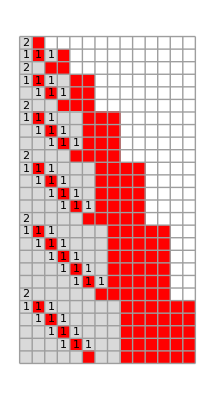


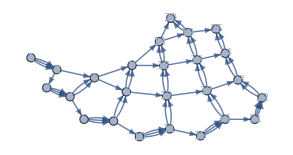
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

Simplify

```mathematica
SSS[{"ABA"->"AAB","A"->"ABA"},"AB",25];Simplify
```

1. By default, the display includes both the sessie (on the left) and its causal network (on the right).  The colored cells in the sessie display represent the changing state string, one line per state, with (micro-)time advancing downward.  (Here the gray cells are As and the red cells Bs).  Events correspond to the change from one state to the next.

2. We can dispense with the arrows indicating the direction of the causal connection in the network if the node numbers are given, since the arrow will always point from smaller to larger node number.

3. Although the command above performed 25 steps and so the causal network has 25 events, the SSSMax option can limit the display of the actual sessie to whatever we want, showing only the beginning of the continuing pattern.

(a couple other common options: NetSize --> 200, HighlightMethod --> Dot)